```mathematica
g=Import["/home/justanotherlad/Documents/BTech Degree Project/facebook_combined.txt"];
```

```mathematica
g1=ToExpression[StringSplit[g]]
```

{0,1,0,2,0,3,0,4,0,5,0,6,0,7,0,8,0,9,0,10,0,11,0,12,0,13,0,14,0,176410,4030,4020,4031,4020,4037,4020,4038,4021,4026,4021,4030,4023,4030,4023,4031,4023,4034,4023,4038,4026,4030,4027,4031,4027,4032,4027,4038,4031,4038}
 |  |  |  |

```mathematica
g2=DeleteCases[Flatten[Table[UndirectedEdge[i,j]&&i≠j,{i,0,Max[g1]},{j,i+1,Max[g1]}]],False];
```

```mathematica
g3=DeleteDuplicates[ReplacePart[g1,Table[{{i},{i+1}}->UndirectedEdge[g1[[i]],g1[[i+1]]],{i,1,Length@g1,2}]]]
```

{0<->1,0<->2,0<->3,0<->4,0<->5,0<->6,0<->7,0<->8,0<->9,0<->10,0<->11,0<->12,0<->13,0<->14,88206,4020<->4031,4020<->4037,4020<->4038,4021<->4026,4021<->4030,4023<->4030,4023<->4031,4023<->4034,4023<->4038,4026<->4030,4027<->4031,4027<->4032,4027<->4038,4031<->4038}
 |  |  |  |

```mathematica
intersectpos=With[{disp=Dispatch[Thread[g3->"foo"]]},Flatten@Position[Replace[g2,disp,{1}],"foo"]];
```

```mathematica
g2=ReplacePart[g2,Table[intersectpos[[i]]->DirectedEdge[g2[[intersectpos[[i]],1]],g2[[intersectpos[[i]],2]]],{i,Length[intersectpos]}]];
```

```mathematica
subedges=Select[g2,#[[1]]<500&&#[[2]]<500&];
```

```mathematica
newEdges=Replace[subedges,{DirectedEdge[a_,b_]:>Style[UndirectedEdge[a,b],Red],UndirectedEdge[a_,b_]:> Style[UndirectedEdge[a,b],Blue]},{1}];
```

```mathematica
graph=Graph[newEdges]
```

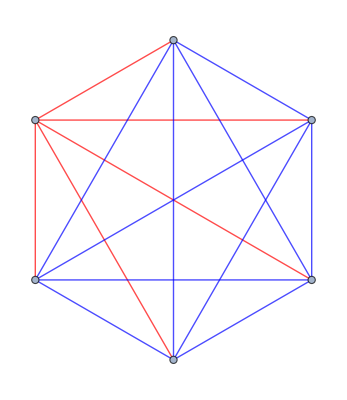

```mathematica
Subgraph[graph,{{0,1,2,3,4,5}}]
```